```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["params.6618764.dat"];
data=Transpose[data][[3;;39]];
Manipulate[ListPlot[data[[n]],PlotRange->All,PlotLegends->{StringJoin["Mean=",ToString[Mean[data[[n]][[a;;50]]]]]},GridLines->{{a},{}}],{n,1,37,1},{a,1,50,1}]
```

Part::take: Cannot take positions 1 through 50 in -40.0244.

ListPlot::lpn: -40.0244 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

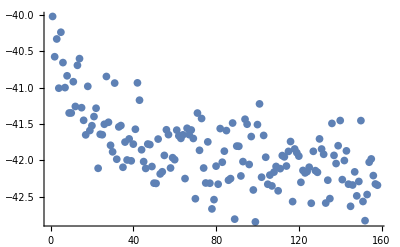

```mathematica
data=Import["eave.6618764.dat"];
data=Transpose[data][[3]];
ListPlot[data]
```